```mathematica
s = 2
xappx = N[1+ (1/Pi)*ArcCos[{-1,-1/2,0, 1/2,1}]]
```

2

{2.,1.66667,1.5,1.33333,1.}

```mathematica
hurwitzData = {{xappx[[1]],HurwitzZeta[s,xappx[[1]]]}, {xappx[[2]],HurwitzZeta[s,xappx[[2]]]}, {xappx[[3]],HurwitzZeta[s,xappx[[3]]]},
{xappx[[4]],HurwitzZeta[s,xappx[[4]]]},
{xappx[[5]],HurwitzZeta[s,xappx[[5]]]}}
```

{{2.,0.644934},{1.66667,0.813875},{1.5,0.934802},{1.33333,1.0956},{1.,1.64493}}

```mathematica
interpHurwitz[x_] = InterpolatingPolynomial[hurwitzData,x]
```

0.644934+(-1.+(0.840527+(-0.788933+0.553055 (-1.33333+x)) (-1.5+x)) (-1.+x)) (-2.+x)

```mathematica
invhurwitzData = {{xappx[[1]],1/HurwitzZeta[s,xappx[[1]]]}, {xappx[[2]],1/HurwitzZeta[s,xappx[[2]]]}, {xappx[[3]],1/HurwitzZeta[s,xappx[[3]]]},
{xappx[[4]],1/HurwitzZeta[s,xappx[[4]]]},
{xappx[[5]],1/HurwitzZeta[s,xappx[[5]]]}}
interpinvHurwitz[x_] = 1/InterpolatingPolynomial[invhurwitzData,x]
```

{{2.,1.55055},{1.66667,1.22869},{1.5,1.06975},{1.33333,0.912744},{1.,0.607927}}

1/(1.55055+(0.942619+(0.0379663+(-0.0257095+0.0134233 (-1.33333+x)) (-1.5+x)) (-1.+x)) (-2.+x))

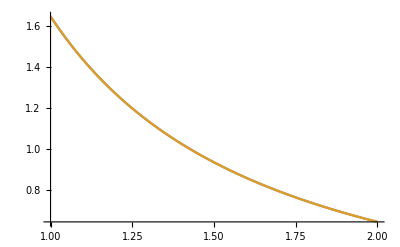

```mathematica
Plot[{HurwitzZeta[s,x],interpinvHurwitz[x]},{x,1,2}]
```

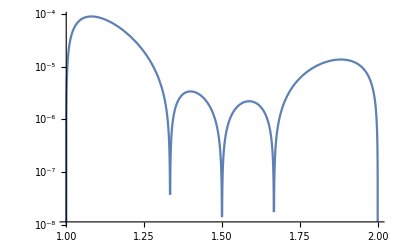

```mathematica
LogPlot[Abs[HurwitzZeta[s,x]-interpinvHurwitz[x]],{x,1,2}]
```

```mathematica
Sum[(m + 1/2)^-r, {m,0,Infinity}]
```

```mathematica
(-1+2^r) Zeta[r]
```

```mathematica
Plot3D[HurwitzZeta[r,k],{k,1,4},{r,1.5,6}]
```

-Graphics3D-

```mathematica
hurwitzZetaAppx[s_,a_,l_] = Sum[(a+m)^-s,{m,0,l}]+ ((a+l+1)^(-s+1))/(s+1) + ((a+l+1)^-s)/2
```

1/2 (1+a+l)^-s+(1+a+l)^(1-s)/(1+s)+HurwitzZeta[s,a]-HurwitzZeta[s,1+a+l]

```mathematica
N[hurwitzZetaAppx[4,1,15]-HurwitzZeta[4,1]]
```

-0.0000273732